```mathematica
Clear[Iter];
Iter[board_]:=ImageConvolve[Image@board, {{1,1,1},{1,20,1},{1,1,1}},Padding->0][[1]]/.{21.->0,22.->1,23.->1,24.->0, 3.->1,_Real->0}
```

```mathematica
Clear[ConwayIter];
ConwayIter[board_,num_]:=NestList[Iter,board, num]
```

```mathematica
ConwayIter[{{0,0,0,0,0},{0,1,1,1,0},{0,0,0,0,0}},10]
```

{{{0,0,0,0,0},{0,1,1,1,0},{0,0,0,0,0}},{{0,0,1,0,0},{0,0,1,0,0},{0,0,1,0,0}},{{0,0,0,0,0},{0,1,1,1,0},{0,0,0,0,0}},{{0,0,1,0,0},{0,0,1,0,0},{0,0,1,0,0}},{«1»},{«1»},{«1»},{{0,0,1,0,0},{0,0,1,0,0},{0,0,1,0,0}},{{0,0,0,0,0},{0,1,1,1,0},{0,0,0,0,0}},{{0,0,1,0,0},{0,0,1,0,0},{0,0,1,0,0}},{{0,0,0,0,0},{0,1,1,1,0},{0,0,0,0,0}}}

```mathematica
Table[0,{i, 10},{j,10}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
tmp=ConwayIter[({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0}}),20]
```

{{{0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}},«19»,{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},«6»,{0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0}}}

```mathematica
Export["test.gif",MatrixPlot/@tmp]
```

test.gif

```mathematica
Directory[]
```

/Users/pjw

```mathematica
Rasterize[#,RasterSize->20]
```

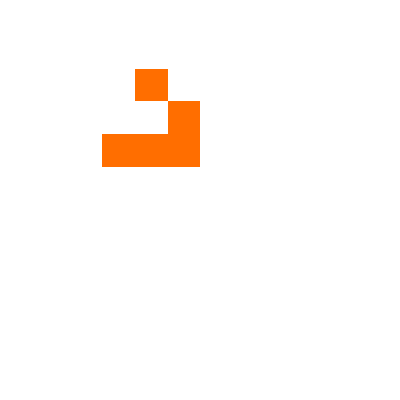

```mathematica
MatrixPlot@tmp[[1]]
```